```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/862nm.dat"]
```

{{1.64105,-0.183658},{1.57964,-0.17595},{1.51907,-0.158773},{1.47433,-0.164981},{1.70936,-0.166019},{1.78557,-0.174341}}

-0.117006-0.0331327 x

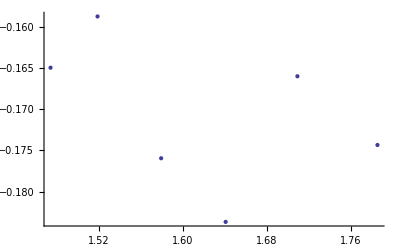

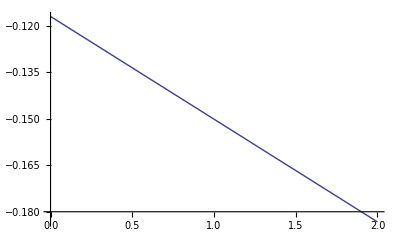

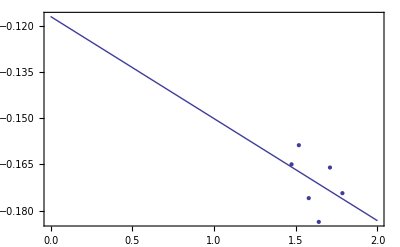

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```